### Time-Dependent Spectra of Quantum Beats

```mathematica
The Matrix Μ and its main properties
```

Matrix analysis of the J = 1/2 to J = 1/2 system (π  transitions).
The master equation in our article is

∂_t ρ̃==-i/ℏ[H,ρ̃]+L_γ ρ̃,

where

L_γ ρ̃==1/2∑_(i,j==1)^2 γ_ij(2 S_i^-ρ̃ S_j^+-S_i^+S_j^-ρ̃-ρ̃ S_i^+S_j^-)+γ_σ/2∑_(i=3)^4 (2 S_i^-ρ̃ S_i^+-S_i^+S_i^-ρ̃-ρ̃ S_i^+S_i^-)

With the above master equation the resulting Bloch equations for the atomic expectation values can be written  compactly as
∂_t ⟨Q(t)⟩==M⟨Q(t)⟩,
whose formal solution is given by
⟨Q(t)⟩==e^Mt⟨Q(0)⟩

Applying the quantum regression formula we get
∂_τ ⟨W(t_1,τ)⟩==M⟨W(t_1,τ)⟩,
whose formal solution is given by
⟨W(t_1,τ)⟩==e^Mτ⟨W(t_1,0)⟩.

The Matrix M is an (8×8) matrix given by

```mathematica
MatrixM[δ_,Δ_,Ω_]:={{-1,-ⅈ Ω,0,0,ⅈ Ω,0,0,0},{-ⅈ Ω,-(1/2+ⅈ Δ),0,0,0,ⅈ Ω,0,0},{0,0,-1,ⅈ Ω,0,0,-ⅈ Ω,0},{0,0,ⅈ Ω,-(1/2+ⅈ(Δ-δ)),0,0,0,-ⅈ Ω},{ⅈ Ω,0,0,0,-(1/2-ⅈ Δ),-ⅈ Ω,0,0},{1/3,ⅈ Ω,2/3,0,-ⅈ Ω,0,0,0},{0,0,-ⅈ Ω,0,0,0,-(1/2-ⅈ(Δ-δ)),ⅈ Ω},{2/3,0,1/3,-ⅈ Ω,0,0,ⅈ Ω,0}}
```

```mathematica
MatrixForm[MatrixM[δ,Δ,Ω]]
```

Here we define the exponential of M as a function of the variable “x”:

```mathematica
ExpM[δ_,Δ_,Ω_,x_]:=MatrixExp[MatrixM[δ,Δ,Ω]*x]
```

```mathematica
(*Here we define the system parameters for resonance fluorescence*)
δ=-7.0;  Δ=0.0;  Ω=6.0;  τmax=30.0;  step1=0.1; step2=0.1;
```

The complete time-dependent EW spectrum is
S(ν,t,Γ)==2ΓRe∫_0^t d t_1 e^(-Γ(t-t_1))∫_0^(t-t_1) dτ e^((Γ/2-iν)τ)[A_13(t_1)A_31(t_1+τ)⟩+A_24(t_1)A_42(t_1+τ)⟩]

To compute the EW spectrum S(ν,t,Γ) we need the correlations
⟨A_13(t_1)A_31(t_1+τ)⟩   and  ⟨A_24(t_1)A_42(t_1+τ)⟩,
which are given by
⟨A_13(t_1)A_31(t_1+τ)⟩==[e^Mτ]_55⟨A_11(t_1)⟩+[e^Mτ]_56⟨A_13(t_1)⟩
⟨A_24(t_1)A_42(t_1+τ)⟩==[e^Mτ]_77⟨A_22(t_1)⟩+[e^Mτ]_78⟨A_24(t_1)⟩

Here we make a list for each matrix element [e^Mτ]_jk as a function of τ:

```mathematica
ExpMtau55=Table[ExpM[δ,Δ,Ω,τ][[5,5]],{τ,0,τmax,step1}];
ExpMtau56=Table[ExpM[δ,Δ,Ω,τ][[5,6]],{τ,0,τmax,step1}];
ExpMtau77=Table[ExpM[δ,Δ,Ω,τ][[7,7]],{τ,0,τmax,step1}];
ExpMtau78=Table[ExpM[δ,Δ,Ω,τ][[7,8]],{τ,0,τmax,step1}];
```

```mathematica
(*ListLinePlot[{Re[ExpMtau55],Re[ExpMtau77],Im[ExpMtau77]},PlotStyle->{Black,Blue,Red},PlotRange->All,Frame->True,ImageSize->800,DataRange->{0,30}]*)
```

The Populations and Coherences for Resonance Fluorescence as a function of  "t" are:
⟨A_11(t)⟩==([e^Mt]_16+[e^Mt]_18)/2,   ⟨A_22(t)⟩==([e^Mt]_36+[e^Mt]_38)/2
⟨A_13(t)⟩==([e^Mt]_26+[e^Mt]_28)/2,    ⟨A_24(t)⟩==([e^Mt]_46+[e^Mt]_48)/2

Here we make a list for each matrix element ⟨A_jk(t)⟩ as a function of t_1:

```mathematica
A11=Table[0.5*ExpM[δ,Δ,Ω,t1][[1,6]]+0.5*ExpM[δ,Δ,Ω,t1][[1,8]],{t1,0,τmax,step2}];
A13=Table[0.5*ExpM[δ,Δ,Ω,t1][[2,6]]+0.5*ExpM[δ,Δ,Ω,t1][[2,8]],{t1,0,τmax,step2}];
A22=Table[0.5*ExpM[δ,Δ,Ω,t1][[3,6]]+0.5*ExpM[δ,Δ,Ω,t1][[3,8]],{t1,0,τmax,step2}];
A24=Table[0.5*ExpM[δ,Δ,Ω,t1][[4,6]]+0.5*ExpM[δ,Δ,Ω,t1][[4,8]],{t1,0,τmax,step2}];
```

For Spontaneous Emission the Populations and Coherences are:
⟨A_11(t)⟩==([e^Mt]_11+[e^Mt]_13)/2 ,             ⟨A_22(t)⟩==([e^Mt]_31+[e^Mt]_33)/2
⟨A_13(t)⟩==([e^Mt]_21+[e^Mt]_23)/2==0,      ⟨A_24(t)⟩==([e^Mt]_41+[e^Mt]_43)/2==0

Here we make a list for each matrix element ⟨A_jk(t)⟩ as a function of t_1:

```mathematica
(*
A11=Table[0.5*ExpM[δ,Δ,Ω,t1][[1,1]]+0.5*ExpM[δ,Δ,Ω,t1][[1,3]],{t1,0,τmax,step2}];
A13=Table[0.5*ExpM[δ,Δ,Ω,t1][[2,1]]+0.5*ExpM[δ,Δ,Ω,t1][[2,3]],{t1,0,τmax,step2}];
A22=Table[0.5*ExpM[δ,Δ,Ω,t1][[3,1]]+0.5*ExpM[δ,Δ,Ω,t1][[3,3]],{t1,0,τmax,step2}];
A24=Table[0.5*ExpM[δ,Δ,Ω,t1][[4,1]]+0.5*ExpM[δ,Δ,Ω,t1][[4,3]],{t1,0,τmax,step2}];
*)
```

Due to temporal factorization in our EW spectrum, we need first to compute four integrals having the structure:

```mathematica
∫_0^(t-Subscript[t, 1]) dτ e^((Γ/2-iν)τ)[e^Mτ]_jk
```

Here we define the four integrals as a function of t and t_1:

```mathematica
Integral55[t_,ν_,Γ_,t1_]:=NIntegrate[Interpolation[
Table[{τmax*(τ)/(Length[ExpMtau55]-1),
Exp[(Γ/2-I*ν)τmax*(τ)/(Length[ExpMtau55]-1)]*ExpMtau55[[τ+1]]},
{τ,0,Length[ExpMtau55]-1,1}],InterpolationOrder->1][τ],
{τ,0.0,t-t1},AccuracyGoal->6,PrecisionGoal->6]

Integral56[t_,ν_,Γ_,t1_]:=NIntegrate[Interpolation[
Table[{τmax*(τ)/(Length[ExpMtau56]-1),
Exp[(Γ/2-I*ν)τmax*(τ)/(Length[ExpMtau56]-1)]*ExpMtau56[[τ+1]]},
{τ,0,Length[ExpMtau56]-1,1}],InterpolationOrder->1][τ],
{τ,0.0,t-t1},AccuracyGoal->6,PrecisionGoal->6]

Integral77[t_,ν_,Γ_,t1_]:=NIntegrate[Interpolation[
Table[{τmax*(τ)/(Length[ExpMtau77]-1),
Exp[(Γ/2-I*ν)τmax*(τ)/(Length[ExpMtau77]-1)]*ExpMtau77[[τ+1]]},
{τ,0,Length[ExpMtau77]-1,1}],InterpolationOrder->1][τ],
{τ,0.0,t-t1},AccuracyGoal->6,PrecisionGoal->6]

Integral78[t_,ν_,Γ_,t1_]:=NIntegrate[Interpolation[
Table[{τmax*(τ)/(Length[ExpMtau78]-1),
Exp[(Γ/2-I*ν)τmax*(τ)/(Length[ExpMtau78]-1)]*ExpMtau78[[τ+1]]},
{τ,0,Length[ExpMtau78]-1,1}],InterpolationOrder->1][τ],
{τ,0.0,t-t1},AccuracyGoal->6,PrecisionGoal->6]
```

Here we define the final EW Spectrum as a function of ν, t, and Γ:

```mathematica
Spectrum[ν_,t_,Γ_]:=2*Γ*NIntegrate[Interpolation[
Table[{t1,
   Exp[-Γ*(t-t1)]*Integral55[t,ν,Γ,t1]*A11[[(t1)/step2+1]]+Exp[-Γ*(t-t1)]*Integral56[t,ν,Γ,t1]*A13[[(t1)/step2+1]]+Exp[-Γ*(t-t1)]*Integral77[t,ν,Γ,t1]*A22[[(t1)/step2+1]]+Exp[-Γ*(t-t1)]*Integral78[t,ν,Γ,t1]*A24[[(t1)/step2+1]]},
{t1,0,t,step2}],InterpolationOrder->1][t1],{t1,0,t},
AccuracyGoal->6,PrecisionGoal->6]
```

### Resonance Fluorescence (RF)

```mathematica
(*The following parameters are the time at which the EW Spectrum is calculated and the filter bandwidth*)
```

```mathematica
t=4; Γ=0.5;
```

Here plot the EW spectrum at an specific time “t” and “Γ” values

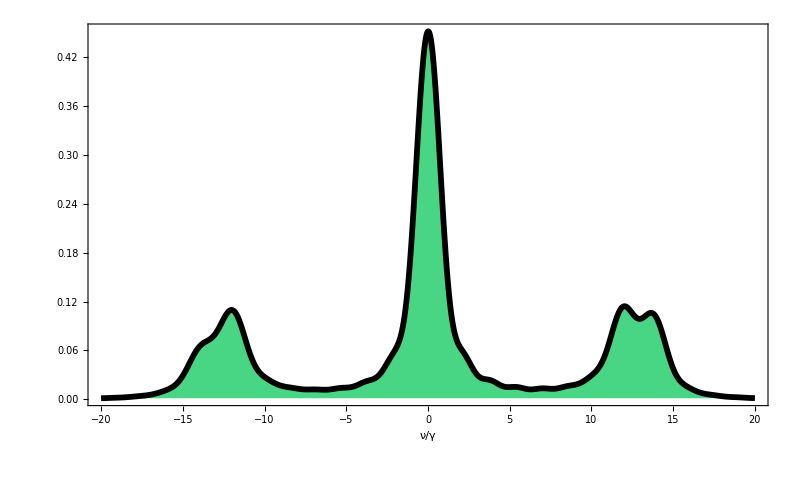
{11.5192,-Graphics-}

```mathematica
ListLinePlot[ParallelTable[{ν,Re[Spectrum[ν,t,Γ]]},{ν,-20,20,0.2}],
PlotRange->All,Frame->{{None,None},{True,None}},FrameStyle->Thick, 
Axes->{True,False},AxesStyle->Thick,FrameTicksStyle->{{{25,Black},25},{{25,Black},25}}, 
FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->Directive[Black,Thickness[0.0052]],
FrameLabel->{{None,None},{Style["ν/γ",30,Black,FontFamily->"Times New Roman"],None}},
Filling->Axis,FillingStyle->Directive[RGBColor[0.1,0.8,0.4],Opacity[0.8]], AspectRatio->0.6,
InterpolationOrder->2, PlotRangePadding->0, ImageSize->800]//AbsoluteTiming
```

Here plot the evolution of the right doublet side band at the frequencies ν= Ω_1, ν=Ω_2 and ν=Ω_av:

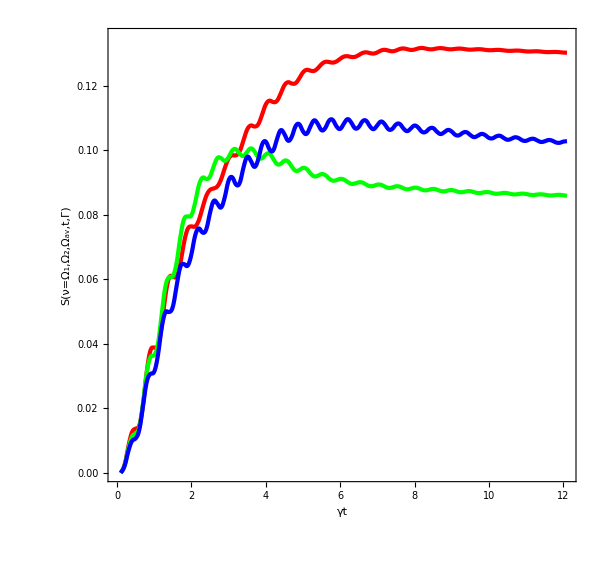
{141.066,-Graphics-}

```mathematica
ListLinePlot[
{ParallelTable[{t,Re[Spectrum[12.00,t,0.5]]},{t,0.1,12.1,0.1}],
ParallelTable[{t,Re[Spectrum[12.95,t,0.5]]},{t,0.1,12.1,0.1}],
ParallelTable[{t,Re[Spectrum[13.90,t,0.5]]},{t,0.1,12.1,0.1}]},
PlotRange->{0,0.135},Frame->True,FrameStyle->Thick, Axes->False,
FrameTicksStyle->{{{20,RGBColor[0.2,0.2,0.2]},20},{{20,RGBColor[0.2,0.2,0.2]},20}}, 
PlotStyle->{Directive[Red,Thickness[0.005]],Directive[Green,Thickness[0.005]],
Directive[Blue,Thickness[0.005]]},
PlotRangePadding->0,InterpolationOrder->2,
FrameLabel->{{Style["S(ν=Ω_1,Ω_2,Ω_av,t,Γ)",27,Black,FontFamily->"Times New Roman"],None},
{Style["γt",28,Black,FontFamily->"Times New Roman"],None}},
ImageSize->600,AspectRatio->0.95]//AbsoluteTiming
```

### The correlation function

The correlation function is
G(t_1,τ)==A_13(t_1)A_31(t_1+τ)⟩+A_24(t_1)A_42(t_1+τ)⟩

```mathematica
(*We will remove the coherent component of the spectrum with the following quantity*)
```

```mathematica
ND=2 Ω^2+(1^2+δ^2)/4+(Δ-δ/2)^2;  IntCohe=Ω^2/ND^2(1^2/4+(Δ-δ/2)^2);
```

Here we define the real and imaginary part of correlation G(t_1,τ):

```mathematica
CorrelationG[t1_]:=Table[
ExpMtau55[[τ+1]]*A11[[t1]]+ExpMtau56[[τ+1]]*A13[[t1]]+ExpMtau77[[τ+1]]*A22[[t1]]+ExpMtau78[[τ+1]]*A24[[t1]],
{τ,0,Length[ExpMtau55]-1,1}]

RealG[t1_]:=ParallelTable[{τmax*(τ)/(Length[ExpMtau55]-1),
Re[CorrelationG[(t1)/step2+1][[τ+1]]]-IntCohe+0.0},
{τ,0,Length[ExpMtau55]-1,1}]

ImaginaryG[t1_]:=ParallelTable[{τmax*(τ)/(Length[ExpMtau55]-1),
Im[CorrelationG[(t1)/step2+1][[τ+1]]]+0.0},
{τ,0,Length[ExpMtau55]-1,1}]
```

Here plot the real and imaginary part of correlation function  G(t_1,τ):

```mathematica
(*Here each time, Subscript[γt, 1] and γτ,  are scaled by γ*)
t1=7;tau=10;
```

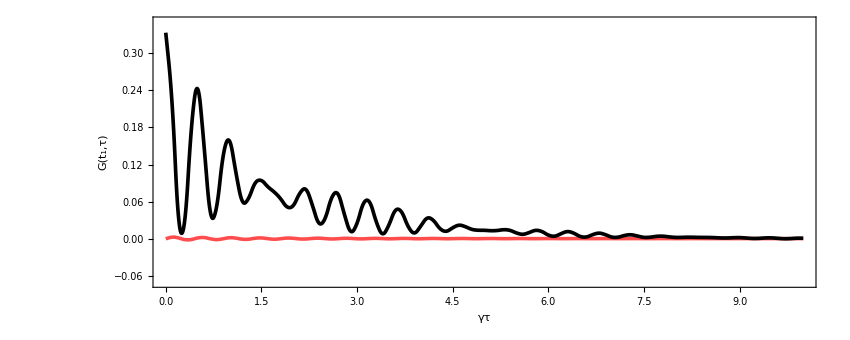

```mathematica
ListLinePlot[{
Take[ImaginaryG[t1],IntegerPart[(tau)/step2+1]],
Take[RealG[t1],IntegerPart[(tau)/step2+1]]},
PlotStyle->{
Directive[Red,Thickness[0.003],Opacity[0.7]],
Directive[Black,Thickness[0.0031],Opacity[1]]},
PlotRange->{-0.07,0.35},InterpolationOrder->2,
Axes->None,Frame->{{True,True},{True,True}},ImageSize->850,
FrameTicksStyle->{{{25,Black},20},{{25,Black},20}}, 
FrameTicks->{{True ,Automatic},{Automatic,Automatic}},
FrameLabel->{Style["γτ",40,Black,FontFamily->"Times New Roman"], 
Style["G(t_1,τ)",30,Black,FontFamily->"Times New Roman"]},
AspectRatio->0.4,PlotRangePadding->0]
```

### Spontaneous Emission (SE)

In this case we have an analytical expression for the EW spectrum

```mathematica
SpectrumSE[Γ_,ν_,t_,γ_,δ_]:=F[Γ,ν,t,0,γ]/((Γ-γ)^2+4 ν^2)+F[Γ,ν,t,δ,γ]/((Γ-γ)^2+4(ν+δ)^2)
F[Γ_,ν_,t_,x_,γ_]:=2Γ (Exp[-Γ t]+Exp[-γ t])-4Γ Exp[-(γ+Γ)t/2]Cos[(ν+x)t]
```

```mathematica
(*Here we define system parameters for Spontaneous Emission*)
δ=-2.0;  Δ=0.0;  Ω=0.0;  τmax=30.0;  step1=0.1; step2=0.1;Γ=0.5;
```

Here we define a list for each trace of the EW spectrum evaluated at specific times

```mathematica
Trace05=ParallelTable[{ν,SpectrumSE[Γ,ν,0.5,1,δ]},{ν,-10,12,0.1}];
Trace1= ParallelTable[{ν,SpectrumSE[Γ,ν,1.0,1,δ]},{ν,-10,12,0.1}];
Trace1p5=ParallelTable[{ν,SpectrumSE[Γ,ν,1.5,1,δ]},{ν,-10,12,0.1}];
Trace2=  ParallelTable[{ν,SpectrumSE[Γ,ν,2.0,1,δ]},{ν,-10,12,0.1}];
Trace2p6=ParallelTable[{ν,SpectrumSE[Γ,ν,2.6,1,δ]},{ν,-10,12,0.1}];
Trace3=ParallelTable[{ν,SpectrumSE[Γ,ν,3.0,1,δ]},{ν,-10,12,0.1}];
Trace4=  ParallelTable[{ν,SpectrumSE[Γ,ν,4.0,1,δ]},{ν,-10,12,0.1}];
Trace5=  ParallelTable[{ν,SpectrumSE[Γ,ν,5.0,1,δ]},{ν,-10,12,0.1}];
Trace6=  ParallelTable[{ν,SpectrumSE[Γ,ν,6.0,1,δ]},{ν,-10,12,0.1}];Trace10=ParallelTable[{ν,SpectrumSE[Γ,ν,10.0,1,δ]},{ν,-10,12,0.1}];Trace15=ParallelTable[{ν,SpectrumSE[Γ,ν,15.0,1,δ]},{ν,-10,12,0.1}];
```

Here we arrange the above lists to plot them in a convenient way

```mathematica
Trace05=   Table[Insert[Trace05[[j]],  19,2],{j,1,Length[Trace05]}];
Trace1=      Table[Insert[Trace1[[j]],    17,2],{j,1,Length[Trace1]}];
Trace1p5=Table[Insert[Trace1p5[[j]],15,2],{j,1,Length[Trace1p5]}];
Trace2=     Table[Insert[Trace2[[j]],      13,2],{j,1,Length[Trace2]}];
Trace2p6= Table[Insert[Trace2p6[[j]], 11,2],{j,1,Length[Trace2p6]}];
Trace3=     Table[Insert[Trace3[[j]],      9.0,2],{j,1,Length[Trace3]}];
Trace4=     Table[Insert[Trace4[[j]],      7,2],{j,1,Length[Trace4]}];
Trace5=     Table[Insert[Trace5[[j]],     5.5,2],{j,1,Length[Trace5]}];
Trace6=     Table[Insert[Trace6[[j]],    4,2],{j,1,Length[Trace6]}];
Trace10=  Table[Insert[Trace10[[j]],  2.5,2],{j,1,Length[Trace10]}];
Trace15=  Table[Insert[Trace15[[j]],    1,2],{j,1,Length[Trace15]}];
```

Here we plot all traces of the Spectrum

```mathematica
Show[Graphics3D[{
Red,Thickness[0.0025],BSplineCurve[Trace15],
Black,Thickness[0.0025],BSplineCurve[Trace10],
RGBColor[0,0.8,0.8],Thickness[0.0025],BSplineCurve[Trace6],
Purple,Thickness[0.0025],BSplineCurve[Trace5],
RGBColor[0,0.7,0.4],Thickness[0.0025],BSplineCurve[Trace4],
Orange,Thickness[0.0025],BSplineCurve[Trace3],
Purple,Thickness[0.0025],BSplineCurve[Trace2p6],
Blue,Thickness[0.0025],BSplineCurve[Trace2],
Black,Thickness[0.0025],BSplineCurve[Trace1p5],
Red,Thickness[0.0025],BSplineCurve[Trace1],
Green,Thickness[0.0025],BSplineCurve[Trace05]
}],
Axes->{True,True,True},PlotRange->All,
Ticks->{{{-10,-10},{0,0},{3,2},{10,10}},{{1,15},{2.5,10},{4,6},{5.5,5},{7,4},{9.0,3},{11,2.6},{13,2},{15,1.5},{17,1},{19,0.5}},Automatic},
TicksStyle->Directive[25,Black],BoxRatios->{3,5.5,2},
Boxed->False,
AxesEdge->{{0,0},{1,0},{1,1}},AxesLabel->{
Style["ν/γ",35,Black,FontFamily->"Times New Roman"],
Style["γt",35,Black,FontFamily->"Times New Roman"],
Rotate[Style["S(ν,t,Γ)",35,Black,FontFamily->"Times New Roman"],π/2]},ImageSize->1000]
```

-Graphics3D-